```mathematica
dispersion[x_,y_] := -2*(Cos[x]+Cos[y])-4*tp*Cos[x]*Cos[y]
```

```mathematica
tp = -0.35;
mu = 8*(tp-2*tp^3);
```

```mathematica
mu
```

-2.114

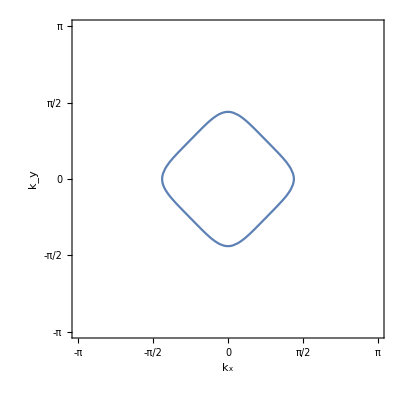

```mathematica
ContourPlot[dispersion[x,y]==mu,{x,-Pi,Pi},{y,-Pi,Pi},Frame->True,FrameStyle->Black,FrameLabel->{"k_x","k_y"},FrameTicks -> {{{-Pi,-Pi/2,0,Pi/2,Pi},None},{{-Pi,-Pi/2,0,Pi/2,Pi},None}}]
```

```mathematica
Solve[dispersion[x,x]==mu,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.795399},{x→0.-1.40327 ⅈ},{x→0.+1.40327 ⅈ},{x→0.795399}}

```mathematica
pt = 0.795399;
```

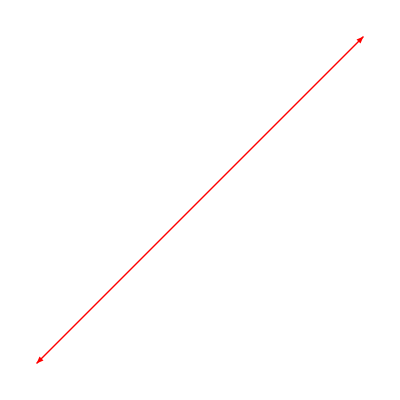

```mathematica
Graphics[{Red,Arrowheads[{-.1,.1}],Arrow[{{-pt,-pt},{pt,pt}}]}]
```

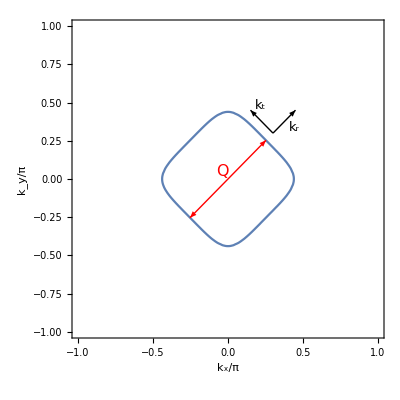

```mathematica
Show[{ContourPlot[dispersion[Pi*x,Pi*y]==mu,{x,-1,1},{y,-1,1},ContourStyle->bl,Frame->True,FrameStyle->Black,FrameLabel->{Style["k_x/π",19,Black,FontFamily->"Times"],Style["k_y/π",19,Black,FontFamily->"Times"]},LabelStyle->Black,FrameTicks -> {Style[{{-1.0,-0.5,0.0,0.5,1.0},None},{{-1,-0.5,0,0.5,1},None}],19}],Graphics[{Red,Arrowheads[{-.05,.05}],Arrow[{{-pt/Pi,-pt/Pi},{pt/Pi,pt/Pi}}],Text[Style["Q",16,FontFamily->"Times"],{-0.04,0.05}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.45,0.45}}],Text[Style["k_r",13,FontFamily->"Times"],{0.44,0.34}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.15,0.45}}],Text[Style["k_t",13,FontFamily->"Times"],{0.22,0.48}]}]}]
```

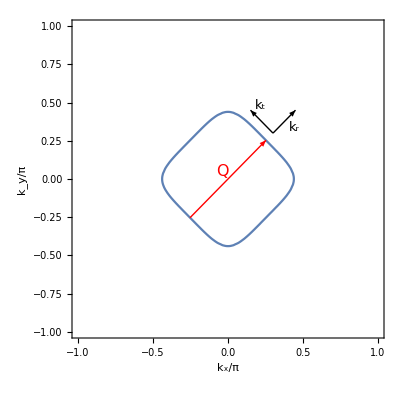

```mathematica
Show[{ContourPlot[dispersion[Pi*x,Pi*y]==mu,{x,-1,1},{y,-1,1},ContourStyle->bl,Frame->True,FrameStyle->Black,FrameLabel->{Style["k_x/π",19,Black,FontFamily->"Times"],Style["k_y/π",19,Black,FontFamily->"Times"]},LabelStyle->Black,FrameTicks -> {Style[{{-1.0,-0.5,0.0,0.5,1.0},None},{{-1,-0.5,0,0.5,1},None}],19}],Graphics[{Red,Arrowheads[{0,.05}],Arrow[{{-pt/Pi,-pt/Pi},{pt/Pi,pt/Pi}}],Text[Style["Q",16,FontFamily->"Times"],{-0.04,0.05}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.45,0.45}}],Text[Style["k_r",13,FontFamily->"Times"],{0.44,0.34}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.15,0.45}}],Text[Style["k_t",13,FontFamily->"Times"],{0.22,0.48}]}]}]
```

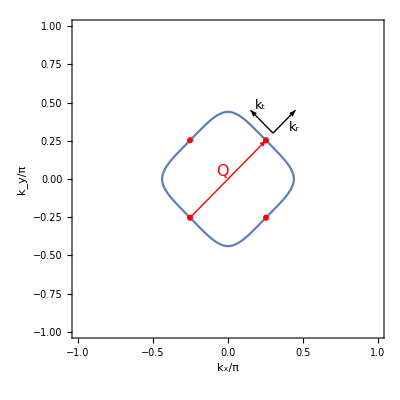

```mathematica
Show[{ContourPlot[dispersion[Pi*x,Pi*y]==mu,{x,-1,1},{y,-1,1},ContourStyle->bl,Frame->True,FrameStyle->Black,FrameLabel->{Style["k_x/π",19,Black,FontFamily->"Times"],Style["k_y/π",19,Black,FontFamily->"Times"]},LabelStyle->Black,FrameTicks -> {Style[{{-1.0,-0.5,0.0,0.5,1.0},None},{{-1,-0.5,0,0.5,1},None}],19}],Graphics[{Red,Arrowheads[{0,.05}],Arrow[{{-pt/Pi,-pt/Pi},{pt/Pi,pt/Pi}}],Text[Style["Q",16,FontFamily->"Times"],{-0.04,0.05}]}],Graphics[{Red,Disk[{-pt/Pi,-pt/Pi},0.02]}],
Graphics[{Red,Disk[{pt/Pi,pt/Pi},0.02]}],Graphics[{Red,Disk[{pt/Pi,-pt/Pi},0.02]}],Graphics[{Red,Disk[{-pt/Pi,pt/Pi},0.02]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.45,0.45}}],Text[Style["k_r",13,FontFamily->"Times"],{0.44,0.34}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.15,0.45}}],Text[Style["k_t",13,FontFamily->"Times"],{0.22,0.48}]}]}]
```